# BooleanFunctionData

Compute data for a boolean function

## Definition

```mathematica
ClearAll[BooleanFunctionData]
BooleanFunctionData[func_]:=<|"BooleanForms"->AssociationMap[BooleanConvert[func,#]&,{"DNF","SOP","CNF","POS","ANF","NOR","NAND","AND","OR","IMPLIES","ITE","IF","BFF","BDT"}],"MinimalBooleanForms"->AssociationMap[BooleanMinimize[func,#]&,{"DNF","SOP","CNF","POS","ANF","NOR","NAND","AND","OR"}],"Table"->BooleanTable[func],"Monotone"->UnateQ[func],"SatisfiableData"-><|"Satisfiable"->SatisfiableQ[func],"SatisfiabilityCount"->SatisfiabilityCount[func],"SatisfiabilityInstances"->SatisfiabilityInstances[func],"Tautology"->TautologyQ[func]|>,"Plot"->RulePlot[func]|>
```

## Documentation

### Usage

MyFunction[arg]

explanation of what use of the argument arg does.

### Details & Options

Additional information about usage and options.

## Examples

### Basic Examples

Text about the example:

```mathematica
MyFunction[x,y]
```

x y

```mathematica
BooleanFunction[100,7]
```

BooleanFunction[…]

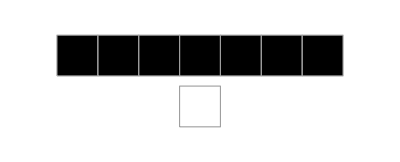
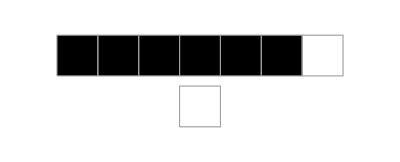
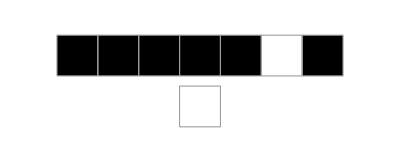
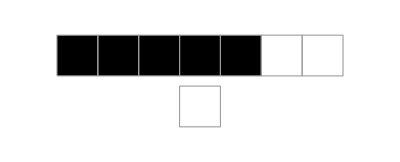
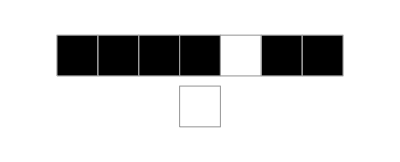
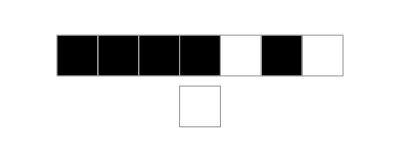
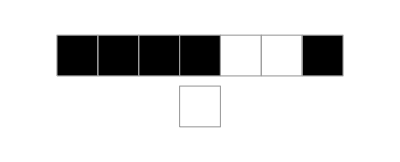
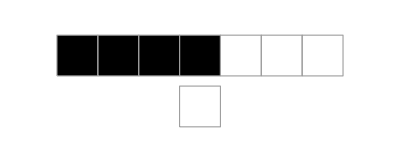
<|BooleanForms→<|DNF→((!#1&&!#2&&!#3&&!#4&&#5&&!#6&&#7)||(!#1&&!#2&&!#3&&!#4&&#6&&!#7)&),SOP→((!#1&&!#2&&!#3&&!#4&&#5&&!#6&&#7)||(!#1&&!#2&&!#3&&!#4&&#6&&!#7)&),CNF→(!#1&&!#2&&!#3&&!#4&&(#5||#6)&&(!#6||!#7)&&(#6||#7)&),POS→(!#1&&!#2&&!#3&&!#4&&(#5||#6)&&(!#6||!#7)&&(#6||#7)&),ANF→((#1&&#6)⊻(#2&&#6)⊻(#3&&#6)⊻(#4&&#6)⊻(#5&&#7)⊻(#6&&#7)⊻(#1&&#2&&#6)⊻(#1&&#3&&#6)⊻(#1&&#4&&#6)⊻(#1&&#5&&#7)⊻(#1&&#6&&#7)⊻(#2&&#3&&#6)⊻(#2&&#4&&#6)⊻(#2&&#5&&#7)⊻(#2&&#6&&#7)⊻(#3&&#4&&#6)⊻(#3&&#5&&#7)⊻(#3&&#6&&#7)⊻(#4&&#5&&#7)⊻(#4&&#6&&#7)⊻(#5&&#6&&#7)⊻(#1&&#2&&#3&&#6)⊻(#1&&#2&&#4&&#6)⊻(#1&&#2&&#5&&#7)⊻(#1&&#2&&#6&&#7)⊻(#1&&#3&&#4&&#6)⊻(#1&&#3&&#5&&#7)⊻(#1&&#3&&#6&&#7)⊻(#1&&#4&&#5&&#7)⊻(#1&&#4&&#6&&#7)⊻(#1&&#5&&#6&&#7)⊻(#2&&#3&&#4&&#6)⊻(#2&&#3&&#5&&#7)⊻(#2&&#3&&#6&&#7)⊻(#2&&#4&&#5&&#7)⊻(#2&&#4&&#6&&#7)⊻(#2&&#5&&#6&&#7)⊻(#3&&#4&&#5&&#7)⊻(#3&&#4&&#6&&#7)⊻(#3&&#5&&#6&&#7)⊻(#4&&#5&&#6&&#7)⊻(#1&&#2&&#3&&#4&&#6)⊻(#1&&#2&&#3&&#5&&#7)⊻(#1&&#2&&#3&&#6&&#7)⊻(#1&&#2&&#4&&#5&&#7)⊻(#1&&#2&&#4&&#6&&#7)⊻(#1&&#2&&#5&&#6&&#7)⊻(#1&&#3&&#4&&#5&&#7)⊻(#1&&#3&&#4&&#6&&#7)⊻(#1&&#3&&#5&&#6&&#7)⊻(#1&&#4&&#5&&#6&&#7)⊻(#2&&#3&&#4&&#5&&#7)⊻(#2&&#3&&#4&&#6&&#7)⊻(#2&&#3&&#5&&#6&&#7)⊻(#2&&#4&&#5&&#6&&#7)⊻(#3&&#4&&#5&&#6&&#7)⊻(#1&&#2&&#3&&#4&&#5&&#7)⊻(#1&&#2&&#3&&#4&&#6&&#7)⊻(#1&&#2&&#3&&#5&&#6&&#7)⊻(#1&&#2&&#4&&#5&&#6&&#7)⊻(#1&&#3&&#4&&#5&&#6&&#7)⊻(#2&&#3&&#4&&#5&&#6&&#7)⊻(#1&&#2&&#3&&#4&&#5&&#6&&#7)⊻#6&),NOR→(#1⊽#2⊽#3⊽#4⊽(#5⊽#6)⊽(!#6⊽!#7)⊽(#6⊽#7)&),NAND→((!#1⊼!#2⊼!#3⊼!#4⊼#5⊼!#6⊼#7)⊼(!#1⊼!#2⊼!#3⊼!#4⊼#6⊼!#7)&),AND→(!#1&&!#2&&!#3&&!#4&&!(!#5&&!#6)&&!(#6&&#7)&&!(!#6&&!#7)&),OR→(!(#1||#2||#3||#4||!#5||#6||!#7)||!(#1||#2||#3||#4||!#6||#7)&),IMPLIES→(!(!#1⇒(!#2⇒(!#3⇒(!#4⇒!((#5⇒!((#6⇒#7)⇒!(!#6⇒!#7)))⇒!(!#5⇒(#6⇒#7)))))))&),ITE→(If[#1,False,If[#2,False,If[#3,False,If[#4,False,If[#5,If[#6,If[#7,False,True],If[#7,True,False]],If[#6,If[#7,False,True],False]]]]]]&),IF→(If[#1,False,If[#2,False,If[#3,False,If[#4,False,If[#5,If[#6,If[#7,False,True],If[#7,True,False]],If[#6,If[#7,False,True],False]]]]]]&),BFF→BooleanFunction[…],BDT→(!#1&&!(#2||(!#2&&(#3||(!#3&&(#4||(!#4&&((#5&&((#6&&#7)||(!#6&&!#7)))||(!#5&&((#6&&#7)||!#6)))))))))&)|>,MinimalBooleanForms→<|DNF→((!#1&&!#2&&!#3&&!#4&&#5&&!#6&&#7)||(!#1&&!#2&&!#3&&!#4&&#6&&!#7)&),SOP→((!#1&&!#2&&!#3&&!#4&&#5&&!#6&&#7)||(!#1&&!#2&&!#3&&!#4&&#6&&!#7)&),CNF→(!#1&&!#2&&!#3&&!#4&&(#5||!#7)&&(!#6||!#7)&&(#6||#7)&),POS→(!#1&&!#2&&!#3&&!#4&&(#5||!#7)&&(!#6||!#7)&&(#6||#7)&),ANF→((#1&&#6)⊻(#2&&#6)⊻(#3&&#6)⊻(#4&&#6)⊻(#5&&#7)⊻(#6&&#7)⊻(#1&&#2&&#6)⊻(#1&&#3&&#6)⊻(#1&&#4&&#6)⊻(#1&&#5&&#7)⊻(#1&&#6&&#7)⊻(#2&&#3&&#6)⊻(#2&&#4&&#6)⊻(#2&&#5&&#7)⊻(#2&&#6&&#7)⊻(#3&&#4&&#6)⊻(#3&&#5&&#7)⊻(#3&&#6&&#7)⊻(#4&&#5&&#7)⊻(#4&&#6&&#7)⊻(#5&&#6&&#7)⊻(#1&&#2&&#3&&#6)⊻(#1&&#2&&#4&&#6)⊻(#1&&#2&&#5&&#7)⊻(#1&&#2&&#6&&#7)⊻(#1&&#3&&#4&&#6)⊻(#1&&#3&&#5&&#7)⊻(#1&&#3&&#6&&#7)⊻(#1&&#4&&#5&&#7)⊻(#1&&#4&&#6&&#7)⊻(#1&&#5&&#6&&#7)⊻(#2&&#3&&#4&&#6)⊻(#2&&#3&&#5&&#7)⊻(#2&&#3&&#6&&#7)⊻(#2&&#4&&#5&&#7)⊻(#2&&#4&&#6&&#7)⊻(#2&&#5&&#6&&#7)⊻(#3&&#4&&#5&&#7)⊻(#3&&#4&&#6&&#7)⊻(#3&&#5&&#6&&#7)⊻(#4&&#5&&#6&&#7)⊻(#1&&#2&&#3&&#4&&#6)⊻(#1&&#2&&#3&&#5&&#7)⊻(#1&&#2&&#3&&#6&&#7)⊻(#1&&#2&&#4&&#5&&#7)⊻(#1&&#2&&#4&&#6&&#7)⊻(#1&&#2&&#5&&#6&&#7)⊻(#1&&#3&&#4&&#5&&#7)⊻(#1&&#3&&#4&&#6&&#7)⊻(#1&&#3&&#5&&#6&&#7)⊻(#1&&#4&&#5&&#6&&#7)⊻(#2&&#3&&#4&&#5&&#7)⊻(#2&&#3&&#4&&#6&&#7)⊻(#2&&#3&&#5&&#6&&#7)⊻(#2&&#4&&#5&&#6&&#7)⊻(#3&&#4&&#5&&#6&&#7)⊻(#1&&#2&&#3&&#4&&#5&&#7)⊻(#1&&#2&&#3&&#4&&#6&&#7)⊻(#1&&#2&&#3&&#5&&#6&&#7)⊻(#1&&#2&&#4&&#5&&#6&&#7)⊻(#1&&#3&&#4&&#5&&#6&&#7)⊻(#2&&#3&&#4&&#5&&#6&&#7)⊻(#1&&#2&&#3&&#4&&#5&&#6&&#7)⊻#6&),NOR→(#1⊽#2⊽#3⊽#4⊽(#5⊽!#7)⊽(!#6⊽!#7)⊽(#6⊽#7)&),NAND→((!#1⊼!#2⊼!#3⊼!#4⊼#5⊼!#6⊼#7)⊼(!#1⊼!#2⊼!#3⊼!#4⊼#6⊼!#7)&),AND→(!#1&&!#2&&!#3&&!#4&&!(!#5&&#7)&&!(#6&&#7)&&!(!#6&&!#7)&),OR→(!(#1||#2||#3||#4||!#5||#6||!#7)||!(#1||#2||#3||#4||!#6||#7)&)|>,Table→{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,True,False,False},Monotone→False,SatisfiableData→<|Satisfiable→True,SatisfiabilityCount→3,SatisfiabilityInstances→{{False,False,False,False,False,True,False}},Tautology→False|>,Plot→-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,QuantifiersEliminated→BooleanFunction[…]|>

```mathematica
BooleanFunctionData[BooleanFunction[100,7]]
```

### Scope

Text about additional examples expanding scope (and see other sections for options, applications, etc):

```mathematica
MyFunction[x,y,z]
```

x y z

### Options

### Applications

### Properties and Relations

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed By

Author Name

### Keywords

keyword 1

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

SymbolName (documented Wolfram Language symbol)

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.